## Dr. Ellen Gethner--CSCI 5451--Mathematica Lab--The Flaw in Kempe's "Proof" of the Four Color Theorem (Double click on the rightmost bar to open the lab)

```mathematica
<<Combinatorica`;
Off[General::spell1];
Off[General::spell];

Clear[myGraph]; myGraph[graph_,imageSize_,caption_,backgroundColor_]:=ShowGraph[graph,VertexNumber->On,VertexStyle->Disk[.045],VertexNumberPosition->Center,VertexColor->Yellow,PlotLabel->caption,ImageSize->imageSize,Background->backgroundColor,BaseStyle->{FontWeight->"Bold",FontSize->15}];

eText[word_,x_,y_,fontSize_]:=Graphics[{Black,Text[word,{x,y},BaseStyle->{FontWeight->"Bold",FontSize->fontSize,FontFamily->"Ariel"}]}];
```

Summary So Far: In class we proved the 6-color theorem for planar graphs (Theorem 6.3) and the 5-color theorem for planar graphs (Theorem 6.5). The latter tells us that 

	Given a planar graph G, and five colors from which to choose,  then we can always find a proper vertex coloring of G that uses at most five colors.

We also "proved" the Four Color Theorem (herein refered to as the FCT), which says that an arbitrary planar graph can be properly colored with at most four colors. Did you believe the alleged proof? I hope not! Were you able to find the flaw? This lab is all about the notorious flaw.

Getting to Know Kempe Chains: To help you warm up, I'll remind you of the definitions of Kempe Chain and  Kempe Chain Switch.

Definition 6.2 [Kempe Chain] Let G be a connected graph that has been properly vertex colored. Suppose c_1and c_2 are two of the colors used in the vertex coloring of G. Suppose v∈V(G) is colored c_1. Then the  c_1c_2-Kempe chain containing v is the maximal connected component of G that contains v and only vertices colored  c_1or c_2. 

Definition 6.3 [Kempe Chain Switch] Let G be a properly colored graph and suppose K is a c_1c_2-Kempe chain containing v_1; suppose also that v_1is colored c_1. A c_1c_2-Kempe chain switch of K interchanges the colors c_1and c_2 in K.

Recall also that Proposition 6.4 tells us that any Kempe chain switch preserves a proper vertex coloring of a graph.

Exercises: Let's start by doing a few exercises on the precolored graph shown below.

```mathematica
Show[Import["Desktop/KempeChainPractice08.gif"],ImageSize->500]
```

-Graphics-

1. Find the RB-Kempe Chain containing vertex 7. Perform an RB-Kempe Chain Switch.
2. Find the RB-Kempe Chain containing vertex 5. Perform an RB-Kempe Chain Switch.
3. Find the RB-Kempe Chain containing vertex 6. Perform an RB-Kempe Chain Switch.
4. Find the YG-Kempe Chain containing vertex 8. Perform a YG-Kempe Chain Switch.
5. Find the YG-Kempe Chain containing vertex 2. Perform a YG-Kempe Chain Switch.
6. Find the RG-Kempe Chain containing vertex 9. Perform an RG-Kempe Chain Switch.

The flaw in A. B. Kempe's famous alleged proof of the FCT was based on the fact that two Kempe chains could get tangled. Let us formalize that idea with the following defintion. Of course this definition was not given in class since I tried to fake you out with a faulty proof. The next picture should help you decipher the lengthy definition.

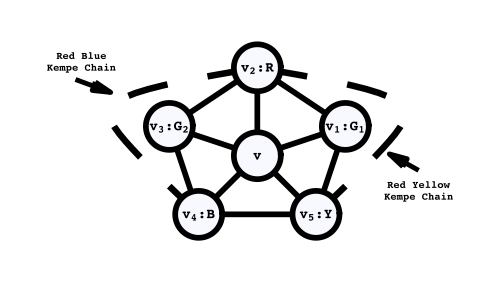

```mathematica
Show[Import["Desktop/KempeDegree5Flaw.pdf"],ImageSize->500]
```

Definition [Irrevocable Kempe Chain Tangle] Let G be a planar graph all of whose vertices, with the exception of one, have been properly vertex colored with four colors. Denote the exceptional vertex by v. Suppose further, that degree(v) = 5, and that the ﬁve neighbors of v (denoted v_1, v_2, v_3, v_4, v_5) are colored in cyclic counterclockwise order (endowed by a plane drawing) by G_1 R G_2 B Y respectively. Moreover, assume that the RB-Kempe chain containing v_2 also contains v_4, and that the RY-Kempe chain containing v_2 also contains v_5. Denote the GB-Kempe chain containing v_1 by KC_1 and the GY-Kempe chain containing v_3 by KC_2 . We say that Kempe’s algorithm causes an 
irrevocable Kempe chain tangle on vertex v if either 

• following a G_1B-Kempe chain switch on KC_1 by a G_2Y -Kempe chain switch on KC_2 causes v_5 to be recolored
Green, or else 

• following a G_2Y -Kempe chain switch on KC_2 by a G_1B-Kempe chain switch on KC_1 causes v_4 to be recolored Green. //end definition

Next let's use our knowledge of the flaw in Kempe's proof.

A Few Historically Motivated Bad Bad Bad Bad Graphs. Now that you have the idea of Kempe chain and Kempe chain switch firmly at hand, let's look at several precolored graphs that illustrate the flaw in Kempe's argument.

Graph 1.

```mathematica
Show[Import["Desktop/HeawoodColoredUnlabelled.gif"],eText[v,400,308,35],ImageSize->700]
```

-Graphics-

The graph above is the dual graph of the map concocted by P.J. Heawood in his famous paper "Map Colour Theorems." Quart. J. Math. 24, 332-338, 1890. 

Notice the five neighbors of vertex v: in counterclockwise order they are colored R B R Y G; not only that but the BY-Kempe Chain contains both neighbors of v colored B and Y, and the BG-Kempe Chain contains both the B and the G neighbors of v.  Before moving on make sure you see those two important Kempe chains.

All good? Now try Kempe's argument in this famous flawed case of the FCT. On the R neighbor directly above v, perform a RG-Kempe chain switch. And on the other R neighbor of v, perform a RY-Kempe Chain switch. According to Kempe's "proof," the color G should no longer be on any of the neighbors of v. Is that so? How about trying the two Kempe chain switches in the other order? Any better? 

So now that we completely and utterly understand the flaw in Kempe's proof, let's investigate further. I'll give you some more historically motivated counterexamples to Kempe's proof. For each one, the vertex labeled v is the one that causes an irrevocable Kempe chain tangle. Do each of the following graphs indeed cause a tangle?

Graph 2. The graph below is due to de la Vallee Poussin in 1896 (and can be found on page 124 of Robin J. Wilson's book Four Colors Suﬃce. Princeton University Press, Princeton, NJ, 2002). Note that one vertex besides v has been left uncolored; that should not affect your investigation.

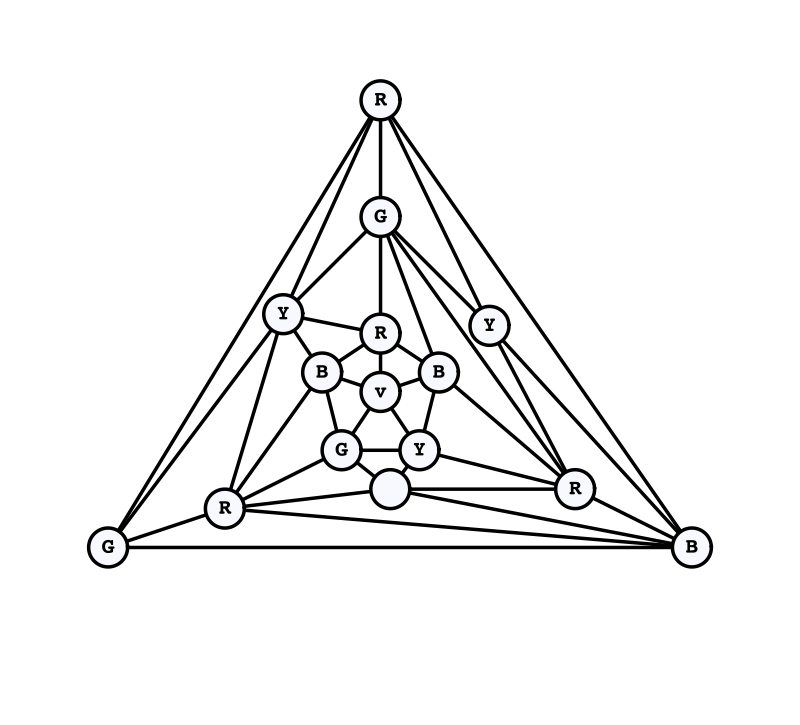

```mathematica
Show[Import["Desktop/PoussinColored.pdf"],ImageSize->800]
```

Graph 3. The next graph and counterexample is due to Rudolf and Gerda Fritsch in their book The Four-Color Theorem, published by Springer-Verlag in 1998. In fact the graph is the dual of the map shown on the front cover of their book! Show that vertex v causes an irrevocable Kempe chain tangle.

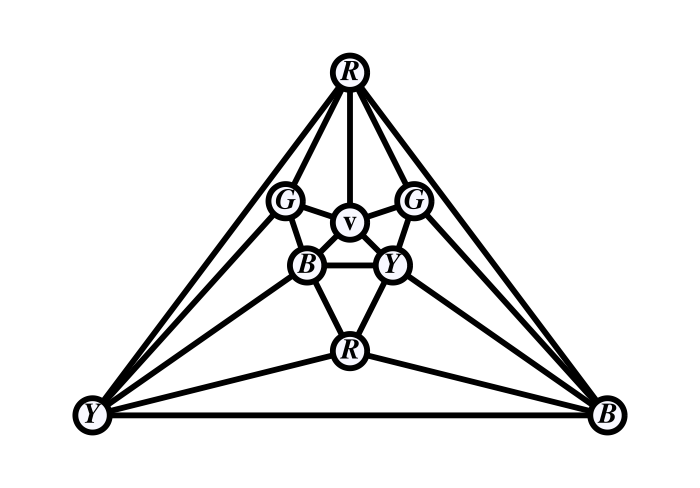

```mathematica
Show[Import["Desktop/fritschColored.pdf"],ImageSize->700]
```

BIG INVESTIGATION FOR THE DAY. Finally, your mission, should you choose to accept it, is to think about what it takes to be a smallest counterexample to Kempe's alleged proof. Errera in his 1921 PhD  (Du Colorage des Cartes et de Quelques d.b4Anaysis Situs. PhD thesis, Gauthier-Villars, Paris) was the first to think about Kempe's induction proof in terms of the numbering that was assigned to the vertices of a planar graph. Different numberings produce a different order of recursion (to a computer scientist, the idea of induction is simply another way of talking about recursion). 

Fact 1. Any planar graph with eight or fewer vertices will always be correctly colored by Kempe's "Algorithm" regardless of the ordering of the vertices.  

[For a proof see How False is Kempe’s Proof of the Four Color Theorem? by Ellen Gethner and William Springer (former UCD student), which can be downloaded here:

http://carbon.cudenver.edu/~egethner/kempe2.pdf]

Question 1. Fritsch's graph F has nine vertices and 21 edges. Can you remove one edge e of F, and find a precoloring of F\e that yields an even smaller counterexample to Kempe's false proof? If so, can you find an ordering of the vertices that would actually lead to your precoloring?  For a meticulous description of Kempe's alleged proof viewed as an algorithm, see the document "kempeAlgorithmOnly.pdf"  for the "ordering the vertices" part of this problem.

Question 2. Can you remove two edges e and f of F, and find a precoloring of F\{e,f} yields an even smaller counterexample to Kempe's false proof? If so, can you find an ordering of vertices that actually leads to your precoloring?

Question 3. What is the largest number of edges k you can remove from Fritsch's graph and such that F\{e_1,e_2,…,e_k} is still a counterexample to Kempe's proof?

Question 4. Can you remove edges from either of Heawood's or de la Valle Poussin's graphs and find precolorings that maintain each as a counterexample to Kempe's alleged proof? 

Question 5. The icosahedral graph I is shown below with a vertex v pre-chosen. Show that any precoloring of vertices of I (with the exception of v) will never lead to an irrevocable Kempe chain tangle. If you can do this, then you have a proof that any ordering of vertices will always lead to a successful 4-coloring under Kempe's algorithm, because all vertices in I are essentially the same by symmetry.

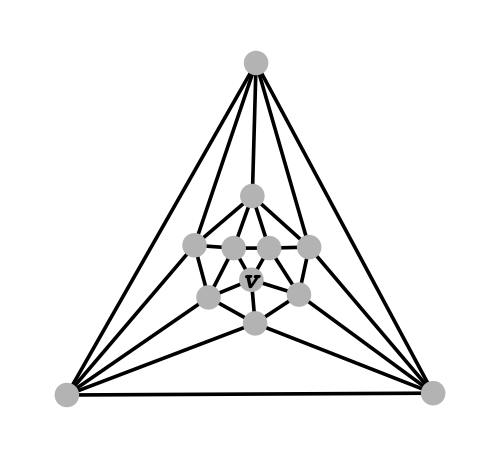

```mathematica
Show[Import["Desktop/icosahedralGraph.pdf"],ImageSize->500]
```